Lab 3

PHYS 2502
[Your Name]

```mathematica
Remove["Global`*"]
```

Solving Equations

```mathematica
equation=(x-2)(x+5)
```

(-2+x) (5+x)

```mathematica
solutions=Solve[expression==0, x]
```

{{x→-5},{x→2}}

```mathematica
solutions[[1]]
```

{x→-5}

```mathematica
(equation/.solutions[[1]])
```

0

```mathematica
(x-2)(x+5)/.{x->-5}
```

0

Table

```mathematica
list1 = {1, 2, 3, 4, 5, 6, 7, 8, 9, 10};
f[x_]:=x*10;
```

```mathematica
table1=Table[{list1[[i]], f[list1[[i]]]}
, {i, 1, 10}]
```

{{1,10},{2,20},{3,30},{4,40},{5,50},{6,60},{7,70},{8,80},{9,90},{10,100}}

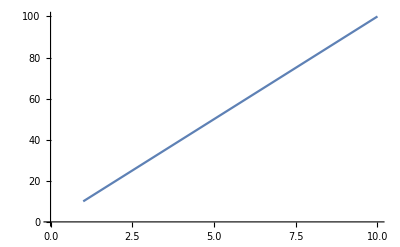

```mathematica
ListLinePlot[table1]
```